# Litaker Data Checking

## Initial setup

Global Variables

```mathematica
litakerData=<||>;
```

Set Directory

```mathematica
SetDirectory["C://Users/kahrendsen2/Box Sync/Research/research/othePeopleData/litakerFaradayRotation"]
FileNames[]
```

C:\Users\kahrendsen2\Box Sync\Research\research\othePeopleData\litakerFaradayRotation

{litaker55And70Data.png,litakerThesisNumberDensityt55AND70.svg,t=100graph.svg,t=100.png,t=40page.svg,t=40.png,t=85graph.svg,t=85.png}

## T=40 image

```mathematica
Import[FileNames["*.png"][[2]]]
```

-Graphics-

Obtain the coordinate locations and set up scaling functions

FittedModel[-7.63512+0.0338889 x]

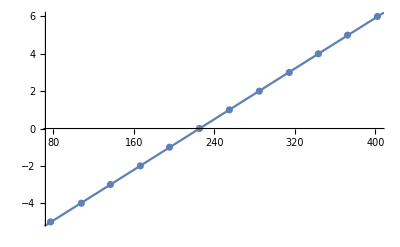

FittedModel[-0.00185105+0.000296766 y]

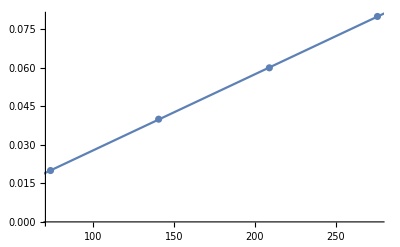

{{390.56,375.478,111.544,96.4617},{68.4016,114.276,163.921,88.5109}}

{5.60054,5.08943,-3.85502,-4.36613}

{0.0184482,0.0320622,0.0467951,0.024416}

{{5.60054,0.0184482},{5.08943,0.0320622},{-3.85502,0.0467951},{-4.36613,0.024416}}

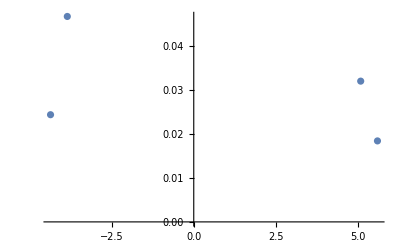

```mathematica
yaxisCoordinates={{62.325174825174834,275.6468531468531},{62.325174825174834,208.89860139860136},{62.325174825174834,140.54195804195808},{62.325174825174834,73.7937062937063}};
yaxisTickMarks=Reverse[{.02,.04,.06,.08}];
xaxisCoordinates={{402.09790209790214,38.8111888111888},{372.3426573426574,38.8111888111888},{343.39160839160843,38.006993006992985},{314.44055944055947,38.006993006992985},{284.6853146853147,38.8111888111888},{254.93006993006998,38.006993006993014},{225.1748251748252,37.2027972027972},{195.41958041958043,38.8111888111888},{166.46853146853147,38.8111888111888},{136.71328671328672,38.8111888111888},{107.76223776223776,38.006993006993014},{77.2027972027972,38.006993006993014}};
xaxisTickMarks=Reverse[Range[-5,6,1]];
xAxisPixels=Transpose[xaxisCoordinates][[1]];
xAxisOrdPairs=Transpose[{xAxisPixels,xaxisTickMarks}];
listPlot=ListPlot[xAxisOrdPairs];
lmx=LinearModelFit[xAxisOrdPairs,x,x]
Show[{ListPlot[xAxisOrdPairs],Plot[lmx[x],{x,0,500}]}]

yAxisPixels=Transpose[yaxisCoordinates][[2]];
yAxisOrdPairs=Transpose[{yAxisPixels,yaxisTickMarks}];
listPlot=ListPlot[yAxisOrdPairs];
lmy=LinearModelFit[yAxisOrdPairs,y,y]
Show[{listPlot,Plot[lmy[y],{y,0,300}]}]

t40NBGdata={{390.56010928961746,68.40163934426226},{375.47814207650276,114.27595628415298},{111.54371584699453,163.92076502732237},{96.46174863387978,88.51092896174862}};
{freqInPixels,angleInPixels}=Transpose[t40NBGdata]
detuningInGHz=lmx["Function"][freqInPixels]
angleInRad=lmy["Function"][angleInPixels]
ordPairs=Transpose[{detuningInGHz,angleInRad}]
AppendTo[litakerData,40-> ordPairs];
ListPlot[ordPairs]
```

## T=100 data

Load in file

```mathematica
Import[FileNames["*.png"][[1]]]
```

-Graphics-

Obtain coordinates and set up scaling functions

FittedModel[-17.1289+0.0707502 x]

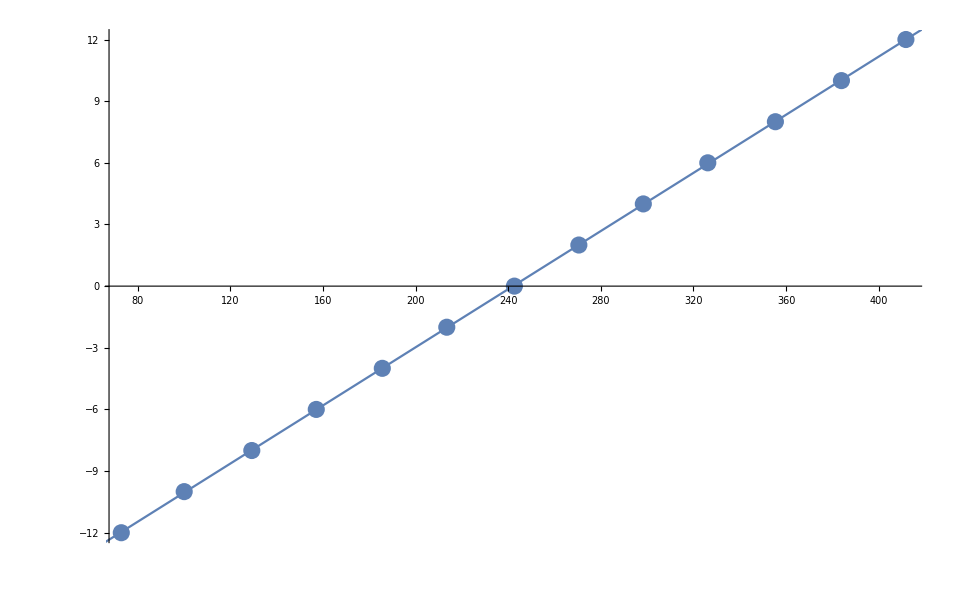

FittedModel[-0.411087+0.0103693 y]

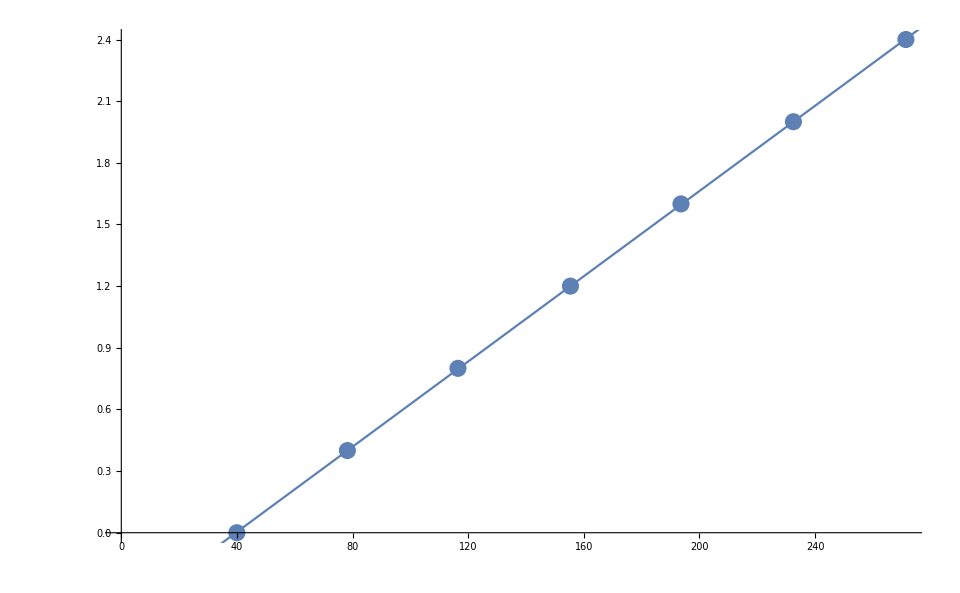

{{398.808,384.553,321.422,314.634,183.621,180.227,99.4474,85.1921},{48.6536,50.0112,128.076,162.696,192.564,160.659,52.7265,49.3324}}

{11.0868,10.0782,5.61174,5.13147,-4.13769,-4.37782,-10.093,-11.1016}

{0.0934173,0.107495,0.916971,1.27596,1.58567,1.25484,0.135651,0.100456}

{{11.0868,0.0934173},{10.0782,0.107495},{5.61174,0.916971},{5.13147,1.27596},{-4.13769,1.58567},{-4.37782,1.25484},{-10.093,0.135651},{-11.1016,0.100456}}

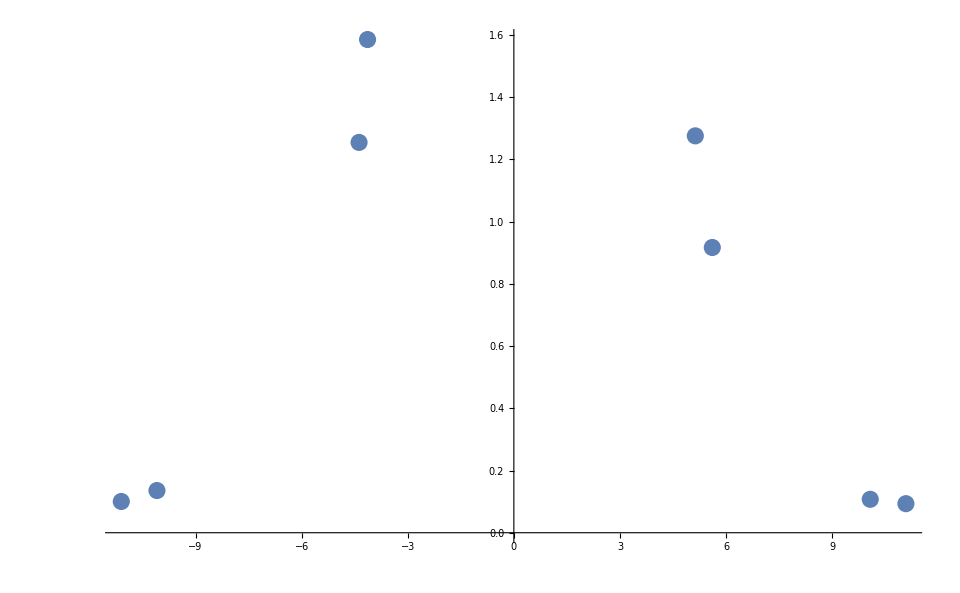

```mathematica
yaxisCoordinates={{57.697547683923716,39.97547683923705},{57.03814713896459,78.2207084468665},{57.03814713896459,116.46594005449592},{57.03814713896459,155.37057220708448},{57.03814713896459,193.61580381471387},{57.03814713896459,232.52043596730243},{57.697547683923716,271.425068119891}};
yaxisTickMarks=Range[0,2.4,.4];
xaxisCoordinates={{411.70546984572235,38.47124824684434},{383.8737727910239,38.47124824684434},{355.36325385694255,38.47124824684434},{326.1739130434783,38.47124824684434},{298.34221598877986,38.47124824684434},{270.5105189340814,38.47124824684434},{242.6788218793829,38.47124824684434},{213.48948106591868,38.47124824684434},{185.65778401122023,38.47124824684434},{157.14726507713885,38.47124824684434},{129.3155680224404,38.47124824684434},{100.12622720897616,38.47124824684434},{72.9733520336606,38.47124824684434}};
xaxisTickMarks=Reverse[Range[-12,12,2]];


xAxisPixels=Transpose[xaxisCoordinates][[1]];
xAxisOrdPairs=Transpose[{xAxisPixels,xaxisTickMarks}];
listPlot=ListPlot[xAxisOrdPairs];
lmx=LinearModelFit[xAxisOrdPairs,x,x]
Show[{ListPlot[xAxisOrdPairs],Plot[lmx[x],{x,0,500}]}]

yAxisPixels=Transpose[yaxisCoordinates][[2]];
yAxisOrdPairs=Transpose[{yAxisPixels,yaxisTickMarks}];
listPlot=ListPlot[yAxisOrdPairs];
lmy=LinearModelFit[yAxisOrdPairs,y,y]
Show[{listPlot,Plot[lmy[y],{y,0,300}]}]

t100data={{398.80785413744746,48.653576437587674},{384.5525946704068,50.01122019635346},{321.4221598877981,128.07573632538575},{314.63394109396916,162.6956521739131},{183.62131837307155,192.56381486676023},{180.2272089761571,160.65918653576443},{99.4474053295933,52.72650771388501},{85.19214586255262,49.33239831697057}};
{freqInPixels,angleInPixels}=Transpose[t100data]
detuningInGHz=lmx["Function"][freqInPixels]
angleInRad=lmy["Function"][angleInPixels]
ordPairs2=Transpose[{detuningInGHz,angleInRad}]
ListPlot[ordPairs2]
AppendTo[litakerData,100-> ordPairs2];
```

## T=55 and 70 data

T=55

```mathematica
files=FileNames["*.png"]
Import["litaker55And70Data.png"]
```

{litaker55And70Data.png,t=100.png,t=40.png,t=85.png}

-Graphics-

FittedModel[-0.331788+0.000800047 y]

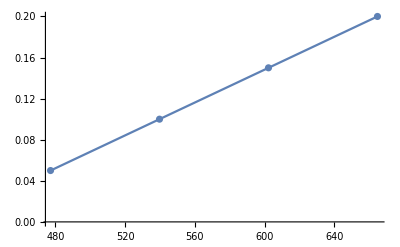

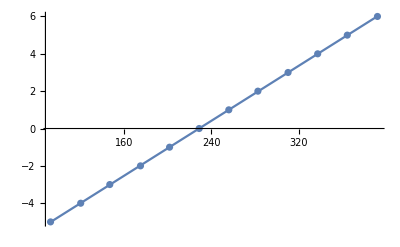

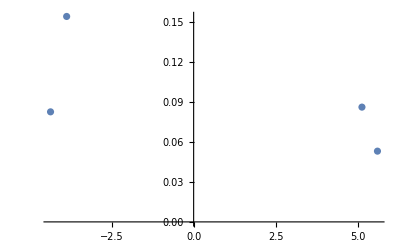

```mathematica
yAxisCoordinates={{78.24341412012646,477.2065331928345},{78.7355110642782,539.7028451001054},{78.7355110642782,602.1991570073762},{78.7355110642782,664.6954689146471}};
yAxisPixels=Transpose[yAxisCoordinates][[2]];
yAxisTickMarks=Range[.05,.2,.05];
yAxisOrderedPairs=Transpose[{yAxisPixels,yAxisTickMarks}];
lmy=LinearModelFit[yAxisOrderedPairs,y,y]
Show[{ListPlot[yAxisOrderedPairs],Plot[lmy[y],{y,yAxisPixels[[1]],yAxisPixels[[-1]]}]}]

xAxisCoordinates={{391.709167544784,446.204425711275},{364.1517386722867,445.71232876712327},{337.086406743941,445.2202318229715},{310.0210748155954,445.71232876712327},{282.4636459430981,446.204425711275},{255.89041095890414,445.71232876712327},{228.8250790305585,445.71232876712327},{201.75974710221288,445.2202318229715},{175.18651211801898,445.2202318229715},{147.1369863013699,444.7281348788198},{120.56375131717598,443.7439409905163},{93.00632244467862,443.7439409905163}};
xAxisPixels=Transpose[xAxisCoordinates][[1]];
xAxisTickMarks=Reverse[Range[-5,6,1]];
xAxisOrderedPairs=Transpose[{xAxisPixels,xAxisTickMarks}];
lmx=LinearModelFit[xAxisOrderedPairs,x,x];
Show[{ListPlot[xAxisOrderedPairs],Plot[lmx[x],{x,xAxisPixels[[1]],xAxisPixels[[-1]]}]}]

t55dataPoints={{380.390937829294,481.14330874604843},{367.59641728134886,522.4794520547945},{110.72181243414121,518.0505795574288},{124.00842992623816,607.6122233930453}};
{detuningInPixels,angleInPixels}=Transpose[t55dataPoints];
detuningInGHz=lmx["Function"][detuningInPixels];
detuningInRadians=lmy["Function"][angleInPixels];
t55OrderedPairs=Transpose[{detuningInGHz,detuningInRadians}];
ListPlot[t55OrderedPairs]
AppendTo[litakerData,55->t55OrderedPairs];
```

T=70

FittedModel[-0.00805588+0.00177168 y]

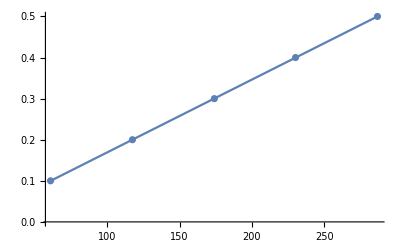

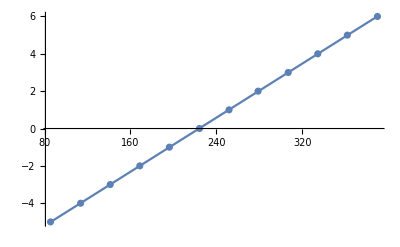

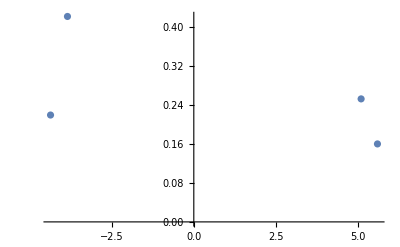

```mathematica
yAxisCoordinates={{69.8777660695469,60.89251844046356},{70.36986301369863,117.48366701791355},{70.36986301369863,174.07481559536353},{70.36986301369863,230.1738672286617},{70.86195995785037,286.76501580611165}};
yAxisPixels=Transpose[yAxisCoordinates][[2]];
yAxisTickMarks=Range[.1,.5,.1];
yAxisOrderedPairs=Transpose[{yAxisPixels,yAxisTickMarks}];
lmy=LinearModelFit[yAxisOrderedPairs,y,y]
Show[{ListPlot[yAxisOrderedPairs],Plot[lmy[y],{y,yAxisPixels[[1]],yAxisPixels[[-1]]}]}]

xAxisCoordinates={{390.2328767123288,60.40042149631188},{362.1833508956797,60.40042149631188},{334.6259220231823,60.40042149631188},{307.06849315068496,60.40042149631188},{279.0189673340359,60.892518440463604},{251.95363540569022,60.40042149631188},{224.39620653319284,60.40042149631188},{196.34668071654374,59.90832455216014},{168.7892518440464,59.90832455216014},{141.231822971549,59.4162276080084},{113.67439409905165,59.90832455216014},{85.62486828240253,59.4162276080084}};
xAxisPixels=Transpose[xAxisCoordinates][[1]];
xAxisTickMarks=Reverse[Range[-5,6,1]];
xAxisOrderedPairs=Transpose[{xAxisPixels,xAxisTickMarks}];
lmx=LinearModelFit[xAxisOrderedPairs,x,x];
Show[{ListPlot[xAxisOrderedPairs],Plot[lmx[x],{x,xAxisPixels[[1]],xAxisPixels[[-1]]}]}]

t70dataPoints={{378.91464699683877,94.84720758693356},{365.13593256059016,147.0094836670179},{117.61116965226554,242.4762908324552},{103.34035827186514,128.3097997892518}};
{detuningInPixels,angleInPixels}=Transpose[t70dataPoints];
detuningInGHz=lmx["Function"][detuningInPixels];
detuningInRadians=lmy["Function"][angleInPixels];
t70OrderedPairs=Transpose[{detuningInGHz,detuningInRadians}];
ListPlot[t70OrderedPairs]
AppendTo[litakerData,70->t70OrderedPairs];
```

## T=85 data

```mathematica
files=FileNames["*.png"]
Import["t=85.png"]
```

{litaker55And70Data.png,t=100.png,t=40.png,t=85.png}

-Graphics-

FittedModel[-0.22684+0.00560134 y]

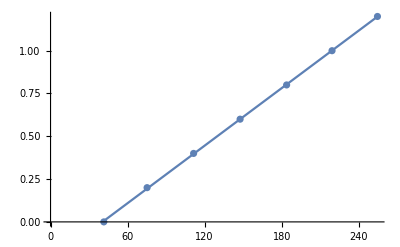

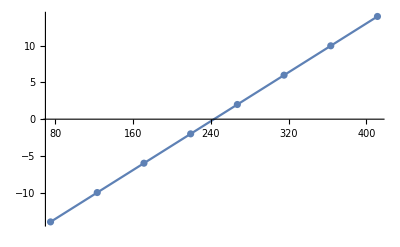

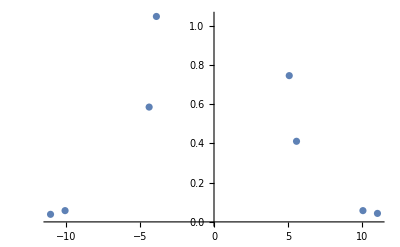

```mathematica
yAxisCoordinates={{62.74367916303402,41.4978204010462},{61.05928509154316,75.18570183086311},{61.05928509154316,111.40017436791635},{61.90148212728859,147.61464690496948},{61.90148212728859,183.82911944202266},{61.90148212728859,219.2013949433304},{61.05928509154316,254.57367044463817}};
yAxisPixels=Transpose[yAxisCoordinates][[2]];
yAxisTickMarks=Range[.00,1.2,.2];
yAxisOrderedPairs=Transpose[{yAxisPixels,yAxisTickMarks}];
lmy=LinearModelFit[yAxisOrderedPairs,y,y]
Show[{ListPlot[yAxisOrderedPairs],Plot[lmy[y],{y,yAxisPixels[[1]],yAxisPixels[[-1]]}]}]

xAxisCoordinates={{411.4132519616391,39.39232781168269},{363.40802092415,39.39232781168269},{315.4027898866609,38.550130775937276},{267.3975588491718,39.39232781168269},{219.39232781168266,39.39232781168269},{171.38709677419357,39.39232781168269},{123.38186573670447,39.39232781168269},{75.37663469921536,39.39232781168269}};
xAxisPixels=Transpose[xAxisCoordinates][[1]];
xAxisTickMarks=Reverse[Range[-14,14,4]];
xAxisOrderedPairs=Transpose[{xAxisPixels,xAxisTickMarks}];
lmx=LinearModelFit[xAxisOrderedPairs,x,x];
Show[{ListPlot[xAxisOrderedPairs],Plot[lmx[x],{x,xAxisPixels[[1]],xAxisPixels[[-1]]}]}]

t85dataPoints={{376.04097646033136,48.2353966870096},{364.2502179598954,50.76198779424587},{310.34960767218837,113.92676547515259},{304.4542284219704,173.7227550130776},{196.65300784655625,227.62336530078468},{190.7576285963383,145.08805579773323},{122.53966870095903,50.76198779424587},{110.74891020052311,47.39319965126418}};
{detuningInPixels,angleInPixels}=Transpose[t85dataPoints];
detuningInGHz=lmx["Function"][detuningInPixels];
detuningInRadians=lmy["Function"][angleInPixels];
t85OrderedPairs=Transpose[{detuningInGHz,detuningInRadians}];
ListPlot[t85OrderedPairs]
AppendTo[litakerData,85->t85OrderedPairs];
```

## Analyzing Data

Define Functions

## Important Physical Constants

```mathematica
nA=1*^-9;
mTorr=1*^-3;
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

(*Physical constants *)
c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(*cm*)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* cm^2*g/s *)
ν0=377107.463;  (* GHz *)
gHzToHz=1*^9;
Q=(re fge k μ)/h;
nDensC=(4 π (ν0*1*^9)^2)/(c  Q);
nDensCLitaker=(4 π ν0*1*^9)/(c Q);


alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;
```

## Rubidium Number Density Functions

```mathematica
ProcessFaradayScanFileFromFileName[fileName_,baselineAngle_,singleCutoff_:12]:=Module[{cutoffs,i,index,file,header, datasetRaw,datasetZeroLineRemoved,datasetNeg,datasetPos,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results,n1pt,det,angle,alldata},
file=ImportFile[fileName];
header=file[[1]];
datasetRaw=file[[2]];
datasetZeroLineRemoved=datasetRaw[Select[#Wavelength>793&]];
dataset=datasetZeroLineRemoved[All,<|#,"DETUNING"->c/100/(#Wavelength)-ν0|>&] ;(* c is in cm/s*)
detAndAngle=dataset[All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&];

$Assumptions=a1>0;
$Assumptions=a2>0;
(*singleCutoff=12;*)
cutoffs={-singleCutoff,singleCutoff};
alldata=Normal[detAndAngle[[All,Values]]];
datasetNeg=Normal[detAndAngle[Select[#DET<cutoffs[[1]]&]][[All,Values]]];
Print[datasetNeg];
datasetPos=Normal[detAndAngle[Select[#DET>cutoffs[[2]]&]][[All,Values]]];
Print[datasetPos];
dataset=Join[datasetPos,datasetNeg];
det=Transpose[dataset][[1]];
angle=Transpose[dataset][[2]];
(* Takes the Maximum and minimum angle of rotation*)
maxmin=MinMax[angle];

i=1;
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelString="A_1/(δ)^2+A_2/(δ)^4+θ_o";
modelA2=a1/(δ)^2+θ0;

model={modelA4,a1>0,a2>0};
startPoints={{a1,1},{a2,1},{θ0,0}};
(*
model={modelA2,a1>0};
startPoints={{a1,1},{θ0,0}};
*)

nlmFit =NonlinearModelFit[Normal[dataset],model,startPoints,δ];
replacements=nlmFit["BestFitParameters"];
fitRangeMin=-30;
fitRangeMax=30;
plot=Plot[Legended[Evaluate[model(*/.(θ0->baselineAngle)*)/.replacements],modelString],{δ,fitRangeMin,fitRangeMax},PlotRange->{Automatic,{Min[maxmin]-.01,Max[maxmin]+.01}},PlotStyle->colorBlindPallete[[i]]];
errors=nlmFit["ParameterErrors"];

n=(a1/.replacements)* nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
n1pt=NumberDensityFromOneMeasurement[angle[[-1]],baselineAngle,det[[-1]],header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
errors=nlmFit["ParameterErrors"];
nErr=errors[[1]]*nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];

finalResult=Show[plot,
ListPlot[
(*Datasets to plot *)
{Legended[Normal[dataset],"Fitted Data Points"],
Legended[Normal[alldata],"All Data Points"]},
(*Plot Options*)
PlotMarkers->{{Graphics[Disk[]],.05},{Graphics[Circle[]],.05}},PlotStyle->colorBlindPallete[[-1]],BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic](*,Epilog->Inset[Style[n,14],{20,.025}]*),AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

results=<|"n_rb"->n/1*^12,"n_rberr"->nErr/1*^12,"n1pt"->n1pt/1*^12,"measuredTheta_0"-> baselineAngle,"calcTheta_0"->θ0/.replacements,"n_rbplot"-> finalResult,"n_rbdataset"->dataset,"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>;
AppendTo[results,header]

];

CalculateNumberDensity[fitParameter_,integratedMagneticField_]:=nDensC*fitParameter/integratedMagneticField;

CalculateNumberDensityLitaker[fitParameter_,integratedMagneticField_]:=nDensCLitaker*fitParameter/integratedMagneticField;
(* The detuning should be input as GHz
The angle should be input as radians
*)
CalculateFittingParameters[faradayRotationOrderedPairs_]:=Module[{startPoints,nlmFit,fitParam},
Clear[a2];
startPoints={{a2,1},{a4,1}};
$Assumptions=a2>0;
$Assumptions=a4>0;
nlmFit =NonlinearModelFit[Normal[faradayRotationOrderedPairs],(a2((δ+ν0)*1*^9)^2)/((δ*1*^9)^2)+(a4((δ+ν0)*1*^9)^2)/((δ*1*^9)^4),startPoints,δ];
fitParam=nlmFit["BestFitParameters"];
fitParam
];

CalculateFittingParametersLitaker[faradayRotationOrderedPairs_]:=Module[{startPoints,nlmFit,fitParam},
Clear[a2];
startPoints={{a2,600},{a4,0}};
$Assumptions=a2>0;
$Assumptions=a4>0;
nlmFit =NonlinearModelFit[Normal[faradayRotationOrderedPairs],{(a2(δ+ν0)*1*^9)/((δ*1*^9)^2)+(a4(δ+ν0)*1*^9)/((δ*1*^9)^4),a2>0,a4>0},startPoints,δ];
nlmFit
];

NumberDensityFromOneMeasurement[rotatedAngle_,baselineAngle_,detuning_,voltage1_,voltage2_]:=
(* Angle should be input in radians *)
((rotatedAngle-baselineAngle)*2*h*(detuning*gHzToHz)^2)/(μ*re*fge*c*k*CalculateIntegratedMagneticField[voltage1,voltage2] );
```

Process Litaker Data

```mathematica
litakerData=KeySortBy[litakerData,Plus]
```

<|40→{{5.60054,0.0184482},{5.08943,0.0320622},{-3.85502,0.0467951},{-4.36613,0.024416}},55→{{5.59466,0.0531496},{5.12257,0.0862205},{-4.35559,0.0826772},{-3.86534,0.154331}},70→{{5.59886,0.159983},{5.10054,0.252398},{-3.85138,0.421534},{-4.3675,0.219268}},85→{{11.0526,0.0433431},{10.0702,0.0574954},{5.57895,0.411303},{5.08772,0.74624},{-3.89474,1.04816},{-4.38596,0.585848},{-10.0702,0.0574954},{-11.0526,0.0386257}},100→{{11.0868,0.0934173},{10.0782,0.107495},{5.61174,0.916971},{5.13147,1.27596},{-4.13769,1.58567},{-4.37782,1.25484},{-10.093,0.135651},{-11.1016,0.100456}}|>

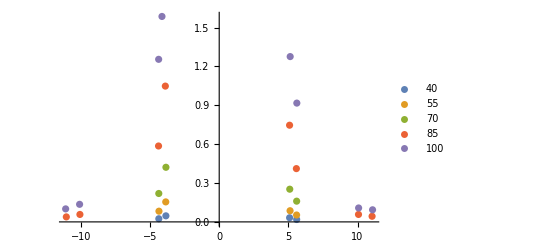

```mathematica
ListPlotAssociationOfLists[litakerData]
```

```mathematica
ListPlotAssociationOfLists[association_]:=Module[{dataSets,dataSetLabels,i},
dataSets={};
dataSetLabels={};
For[i=1,i≤Length[association],i++,
AppendTo[dataSets,association[[i]]];
AppendTo[dataSetLabels,Keys[association][[i]]];
];
ListPlot[dataSets,PlotLegends->dataSetLabels]
];
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

<|40→1.06321×10^12,55→3.36231×10^12,70→9.29801×10^12,85→2.40892×10^13,100→4.47337×10^13|>

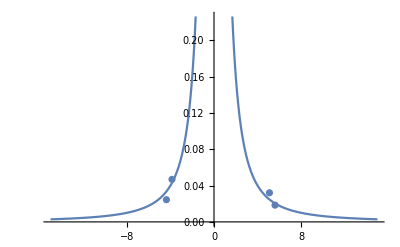
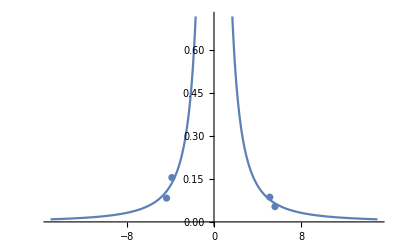
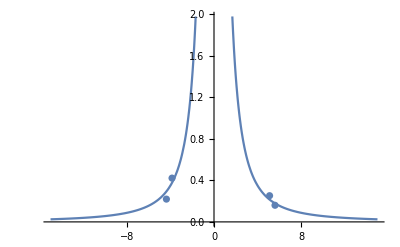
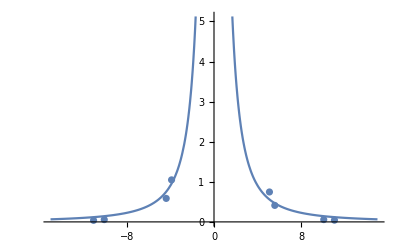
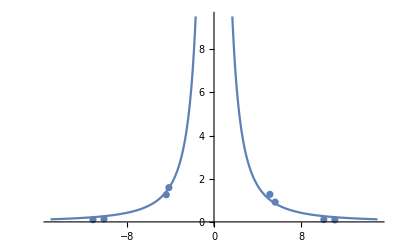
<|40→-Graphics-,55→-Graphics-,70→-Graphics-,85→-Graphics-,100→-Graphics-|>

<|40→1.48325×10^11,55→4.03871×10^11,70→1.13927×10^12,85→2.1688×10^12,100→2.89391×10^12|>

```mathematica
litakerDensitiesRecheck=<||>;
litakerRecheckGraphs=<||>;
errors=<||>;
For[i=1,i≤Length[litakerData],i++,
nlmFit=CalculateFittingParametersLitaker[litakerData[[i]]];
nDen=CalculateNumberDensityLitaker[a2/.nlmFit["BestFitParameters"],200*7];
AppendTo[litakerDensitiesRecheck,Keys[litakerData][[i]]->nDen];
AppendTo[litakerRecheckGraphs,Keys[litakerData][[i]]->Show[{Plot[(a2(δ+ν0)*1*^9)/((δ*1*^9)^2)+(a4(δ+ν0)*1*^9)/((δ*1*^9)^4)/.nlmFit["BestFitParameters"],{δ,-15,15}],ListPlot[litakerData[[i]]]}]];
AppendTo[errors,Keys[litakerData][[i]]->CalculateNumberDensityLitaker[nlmFit["ParameterErrors"][[1]],200*7]];
]
litakerDensitiesRecheck
litakerRecheckGraphs
errors
```

```mathematica
litakerDensities=<|40-> 5.2*^10,55->1.5*^11,70->7.*^11,85->3.5*^12,100->6.0*^12|>
```

<|40→5.2×10^10,55→1.5×10^11,70→7.×10^11,85→3.5×10^12,100→6.×10^12|>

```mathematica
Values[litakerDensitiesRecheck]
Values[litakerDensities]
```

{1.06321×10^12,3.36231×10^12,9.29801×10^12,2.40892×10^13,4.47337×10^13}

{5.2×10^10,1.5×10^11,7.×10^11,3.5×10^12,6.×10^12}

```mathematica
calculationDifferences=AssociationThread[Keys[litakerDensities]->Values[litakerDensitiesRecheck]/Values[litakerDensities]]
```

<|40→20.4463,55→22.4154,70→13.2829,85→6.88263,100→7.45561|>

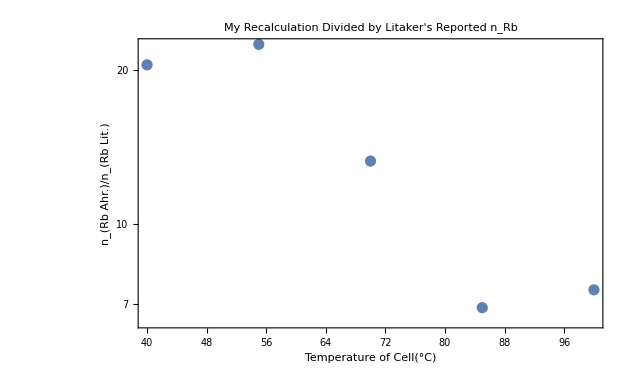

```mathematica
ListLogPlot[calculationDifferences,Frame->True,LabelStyle->22,PlotLabel->"My Recalculation Divided by\nLitaker's Reported n_Rb" ,FrameLabel->{"Temperature of Cell(°C)","n_(Rb Ahr.)/n_(Rb Lit.)"}]
```